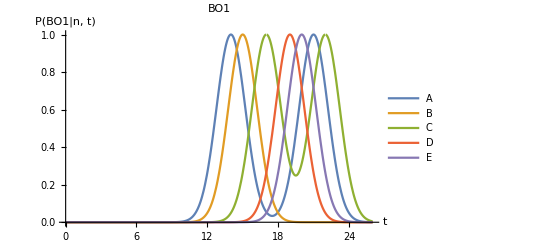

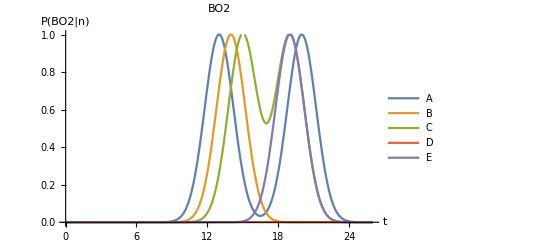

BO1

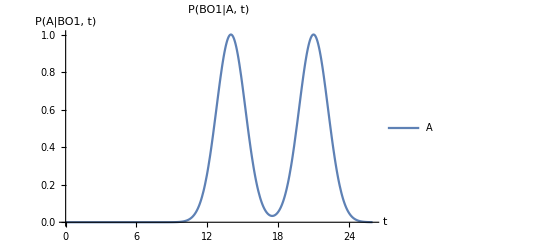

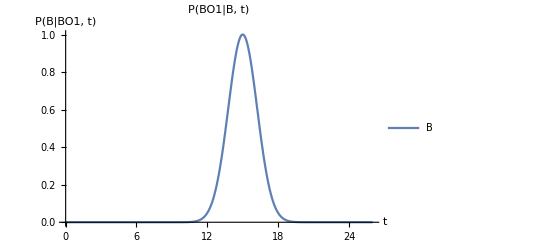

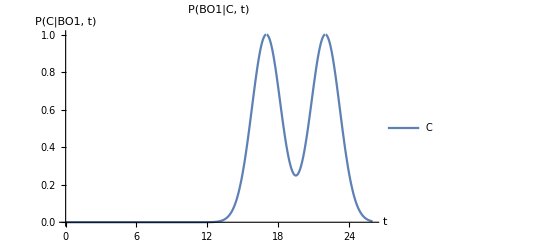

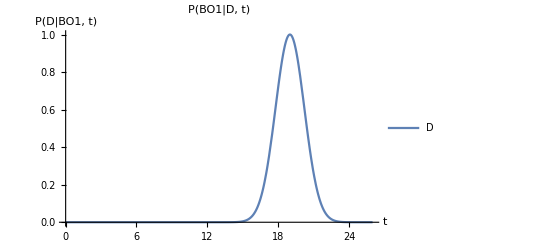

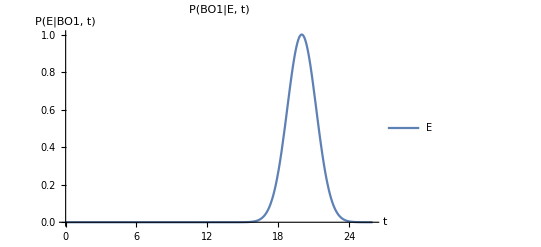

BO1

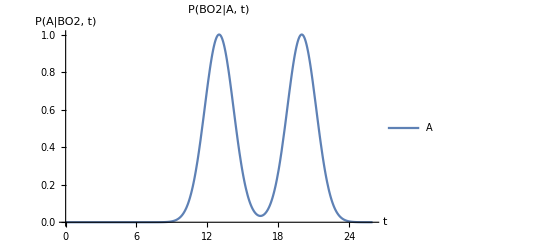

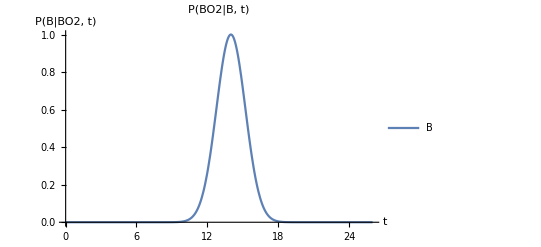

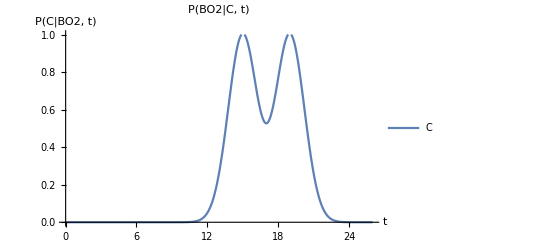

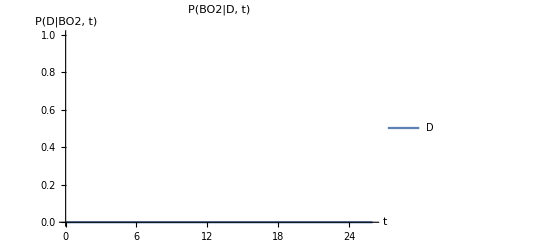

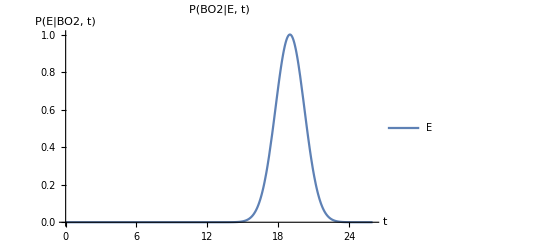

/Users/Rogiel/Dropbox/Shared folders/Projeto de Diplomação/Testes/Distribuição de Probabilidade.nb.pdf

```mathematica
σ=3;
ABO1=Exp[(-(t-14)^2)/σ]+Exp[(-(t-21)^2)/σ];
BBO1=Exp[(-(t-15)^2)/σ];
CBO1=Exp[(-(t-17)^2)/σ]+Exp[(-(t-22)^2)/σ];
DBO1=Exp[(-(t-19)^2)/σ];
EBO1=Exp[(-(t-20)^2)/σ];

ABO2=Exp[(-(t-13)^2)/σ]+Exp[(-(t-20)^2)/σ];
BBO2=Exp[(-(t-14)^2)/σ];
CBO2=Exp[(-(t-15)^2)/σ]+Exp[(-(t-19)^2)/σ];
DBO2=0;
EBO2=Exp[(-(t-19)^2)/σ];

Plot[{ABO1, BBO1, CBO1,DBO1, EBO1}, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(BO1|n, t)"}, PlotLegends->{"A", "B", "C", "D", "E"}, PlotLabel->"BO1"]
Plot[{ABO2, BBO2, CBO2, DBO2, EBO2}, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(BO2|n)"}, PlotLegends->{"A", "B", "C", "D", "E"}, PlotLabel->"BO2"]

Print[Style["BO1", "Title"]]
Plot[ABO1, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(A|BO1, t)"}, PlotLegends->{"A"}, PlotLabel->"P(BO1|A, t)"]
Plot[BBO1, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(B|BO1, t)"}, PlotLegends->{"B"}, PlotLabel->"P(BO1|B, t)"]
Plot[CBO1, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(C|BO1, t)"}, PlotLegends->{"C"}, PlotLabel->"P(BO1|C, t)"]
Plot[DBO1, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(D|BO1, t)"}, PlotLegends->{"D"}, PlotLabel->"P(BO1|D, t)"]
Plot[EBO1, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(E|BO1, t)"}, PlotLegends->{"E"}, PlotLabel->"P(BO1|E, t)"]

Print[Style["BO1", "Title"]]
Plot[ABO2, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(A|BO2, t)"}, PlotLegends->{"A"}, PlotLabel->"P(BO2|A, t)"]
Plot[BBO2, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(B|BO2, t)"}, PlotLegends->{"B"}, PlotLabel->"P(BO2|B, t)"]
Plot[CBO2, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(C|BO2, t)"}, PlotLegends->{"C"}, PlotLabel->"P(BO2|C, t)"]
Plot[DBO2, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(D|BO2, t)"}, PlotLegends->{"D"}, PlotLabel->"P(BO2|D, t)"]
Plot[EBO2, {t, 0 , 26}, PlotRange->{0, 1}, AxesLabel->{"t", "P(E|BO2, t)"}, PlotLegends->{"E"}, PlotLabel->"P(BO2|E, t)"]

Export[ NotebookFileName[]<>".pdf",EvaluationNotebook[]]
```